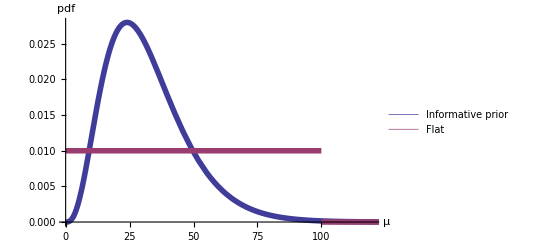

```mathematica
p1 = Plot[{PDF[GammaDistribution[4,8],x],PDF[UniformDistribution[{0,100}],x]},{x,0,150},PlotStyle->{Thickness[0.01]},AxesLabel->{μ,pdf},BaseStyle->{FontSize->16},PlotRange->{{0,120}},PlotLegends->Placed[{"Informative prior","Flat"},Below]]
```

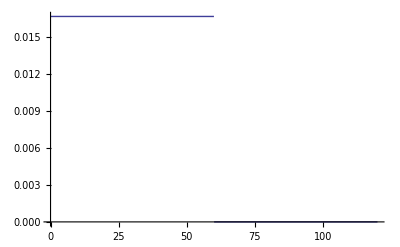

```mathematica
p2 = Plot[PDF[UniformDistribution[{0,60}],x],{x,0,120}]
```